## Canonicity factors

Creating proper inertia factors A_2 and A_3 from the value of A_1

```mathematica
ClearAll["Global`*"]
```

```mathematica
T[j_,gm_]:=1/(j(j+1))√3(√3 Cos[gm]+Sin[gm]);
TP[j_,gm_]:=1/(j(j+1))2 √3 Sin[gm];
S[I_,j_]:=(2I-1-2j)/(2I-1);
SP[I_,j_]:=(2j-1-2I)/(2j-1);
```

```mathematica
A3condition[A1_,I_,j_,V_,gm_]:=(SP[I,j]*A1-V*T[j,gm]);
A2condition[A1_,I_,j_,V_,gm_]:=(SP[I,j]*A1-V*TP[j,gm]);
```

```mathematica
A1=0.2;
I0=35/2;
j0=13/2;
V0=3;
gm0=25;
gammaconst=25;
```

```mathematica
k1[I_,j_,A1_,A2_,A3_]:=(I^2*((2I-1)(A2-A1)+2j*A1)/((2I-1)(A3-A1)+2j*A1))^(1/4);
k1[35/2,j0,A1,2A1,5A1]
k1[35/2,j0,A1,5A1,2A1]
A2condition[A1,0.5,j0,V0,gm0*π/180]
A3condition[A1,0.5,j0,V0,gm0*π/180]
```

3.13507

5.58202

0.0932415

-0.029031

## Generate lists for numerical data

```mathematica
(*the data set for ordering A3>A2>A1 *)
k1data1=Table[{x,k1[x,j0,A1,2A1,5A1]},{x,0.5,45.5,2}];
(*the data set for ordering A2>A3>A1 *)
k1data2=Table[{x,k1[x,j0,A1,5A1,2A1]},{x,0.5,45.5,2}];
```

```mathematica
k1data1
```

{{0.5,0.707107},{2.5,1.38351},{4.5,1.75331},{6.5,2.0399},{8.5,2.28395},{10.5,2.50093},{12.5,2.69866},{14.5,2.88172},{16.5,3.0531},{18.5,3.21484},{20.5,3.36848},{22.5,3.51516},{24.5,3.65575},{26.5,3.79099},{28.5,3.92146},{30.5,4.04763},{32.5,4.16991},{34.5,4.28864},{36.5,4.40412},{38.5,4.51661},{40.5,4.62634},{42.5,4.73349},{44.5,4.83824}}

```mathematica
k1data2
```

{{0.5,0.707107},{2.5,1.807},{4.5,2.56658},{6.5,3.18643},{8.5,3.72163},{10.5,4.19843},{12.5,4.63192},{14.5,5.03171},{16.5,5.40435},{18.5,5.75456},{20.5,6.08583},{22.5,6.40086},{24.5,6.70176},{26.5,6.99025},{28.5,7.2677},{30.5,7.53528},{32.5,7.79394},{34.5,8.04451},{36.5,8.28769},{38.5,8.52408},{40.5,8.75423},{42.5,8.97858},{44.5,9.19757}}

```mathematica
k1plot=ListPlot[{k1data1,k1data2},AspectRatio->0.8,Frame->True,Joined->True,PlotMarkers->{Automatic, Medium},FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Blue,Thick}},PlotRange->Full,FrameLabel->{"I [ℏ]","k_1"},LabelStyle->{18,Bold,Black,FontFamily->"Arial"},ImageSize->380,PlotLegends->Placed[{"A_3>A_2>A_1","A_2>A_3>A_1"},{0.75,0.25}]];
k1fig=Show[k1plot,Graphics[{Magenta,Thickness[0.009],Dashed,Line[{{13/2,0},{13/2,10}}]}],Graphics[{Gray,HatchFilling[-1],Opacity[0.4],Rectangle[{-1,-1},{13/2,10}]}],Graphics[{Green,Opacity[0.11],Rectangle[{13/2,-1},{50,10}]}],Graphics[Inset[Style["I ≤ j",Black,Bold,FontFamily->"Palatino",21],Scaled[{0.08,0.8}]]],Graphics[Inset[Style["I ≥ j",Black,Bold,FontFamily->"Palatino",21],Scaled[{0.3,0.8}]]]];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/wobbling-frequency-algebraic/k1_factor.pdf",k1fig,ImageResolution->800];
k1fig
```

-Graphics-

### k1[I_,j_,A1_,A2_,A3_]:=(I^2*((2I-1)(A2-A1)+2j*A1)/((2I-1)(A3-A1)+2j*A1))^(1/4);

```mathematica
A3extended[I_,j_,V_,gm_]:=SP[I,j]*A1-V*T[j,gm];
A2extended[I_,j_,V_,gm_]:=SP[I,j]*A1-V*TP[j,gm];
k2[I_,j_,A1_,A2_,A3_,V_,gm_]:=(j^2*((2j-1)(A2-A1)+2I*A1+V*(2j-1)/(j(j+1))2 √3 Sin[gm])/((2j-1)(A3-A1)+2I*A1+V*(2j-1)/(j(j+1))√3(√3 Cos[gm]+Sin[gm])))^(1/4);
A1
A2extended[I0,j0,V0,gm0*π/180]
A3extended[I0,j0,V0,gm0*π/180]
```

0.2

-0.473425

-0.595698

## Generate the numerical data

```mathematica
k2data1=Table[{x,k2[x,j0,A1,2A1,5A1,V0,gm0*π/180]},{x,0.5,45.5,2}];
k2data2=Table[{x,k2[x,j0,A1,5A1,2A1,V0,gm0*π/180]},{x,0.5,45.5,2}];
```

```mathematica
k2data1
```

{{0.5,1.88386},{2.5,1.94798},{4.5,1.99989},{6.5,2.04299},{8.5,2.07946},{10.5,2.11078},{12.5,2.13803},{14.5,2.16197},{16.5,2.1832},{18.5,2.20215},{20.5,2.21919},{22.5,2.2346},{24.5,2.24861},{26.5,2.2614},{28.5,2.27314},{30.5,2.28393},{32.5,2.29391},{34.5,2.30315},{36.5,2.31174},{38.5,2.31974},{40.5,2.32722},{42.5,2.33422},{44.5,2.34079}}

```mathematica
k2data2
```

{{0.5,3.07403},{2.5,3.01806},{4.5,2.97317},{6.5,2.93631},{8.5,2.90546},{10.5,2.87925},{12.5,2.85669},{14.5,2.83705},{16.5,2.81981},{18.5,2.80453},{20.5,2.79091},{22.5,2.77868},{24.5,2.76764},{26.5,2.75762},{28.5,2.74848},{30.5,2.74012},{32.5,2.73244},{34.5,2.72536},{36.5,2.7188},{38.5,2.71272},{40.5,2.70707},{42.5,2.70179},{44.5,2.69686}}

```mathematica
k2plot=ListPlot[{k2data1,k2data2},AspectRatio->0.8,Frame->True,Joined->True,PlotMarkers->{Automatic, Medium},FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Blue,Thick}},PlotRange->Full,FrameLabel->{"I [ℏ]","k_2"},LabelStyle->{18,Bold,Black,FontFamily->"Arial"},ImageSize->400,PlotLegends->Placed[{"A_3>A_2>A_1","A_2>A_3>A_1"},{0.75,0.2}]];
k2fig=Show[k2plot,Graphics[{Magenta,Thickness[0.009],Dashed,Line[{{13/2,0},{13/2,10}}]}],Graphics[{Gray,HatchFilling[-1],Opacity[0.4],Rectangle[{-1,-1},{13/2,10}]}],Graphics[{Green,Opacity[0.1],Rectangle[{13/2,-1},{50,10}]}],Graphics[Inset[Style["I ≤ j",Black,Bold,FontFamily->"Palatino",21],Scaled[{0.08,0.5}]]],Graphics[Inset[Style["I ≥ j",Black,Bold,FontFamily->"Palatino",21],Scaled[{0.3,0.5}]]]];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/wobbling-frequency-algebraic/k2_factor.pdf",k2fig,ImageResolution->800];
k2fig
```

-Graphics-

```mathematica
flabel[x_]:=SetPrecision[x,2]
flabel[3.64543434]
```

3.6

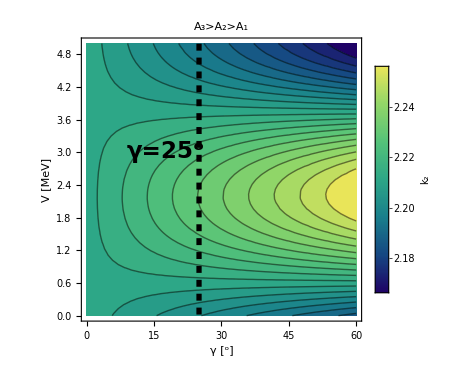

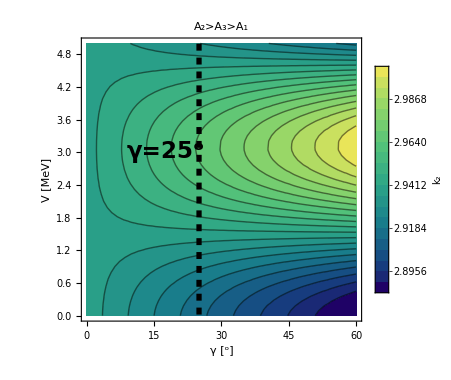

```mathematica
a1test=0.2;
a2test=2*a1test;
a3test=5*a1test;
a2testr=5*a1test;
a3testr=2*a1test;
jtest=13/2;
i0test=35/2;
k2CP[V_,γ_]:=(jtest^2*((2jtest-1)(a2test-a1test)+2*i0test*a1test+V*(2jtest-1)/(jtest(jtest+1))2 √3 Sin[γ])/((2jtest-1)(a3test-a1test)+2*i0test*a1test+V*(2jtest-1)/(jtest(jtest+1))√3(√3 Cos[γ]+Sin[γ])))^(1/4);
k2rCP[V_,γ_]:=(jtest^2*((2jtest-1)(a2testr-a1test)+2*i0test*a1test+V*(2jtest-1)/(jtest(jtest+1))2 √3 Sin[γ])/((2jtest-1)(a3testr-a1test)+2*i0test*a1test+V*(2jtest-1)/(jtest(jtest+1))√3(√3 Cos[γ]+Sin[γ])))^(1/4);
cpk2=ContourPlot[k2CP[x*π/180,y],{x,0,60},{y,0,5},Contours->20,PlotRangePadding->None,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"γ [^o]","V [MeV]"},LabelStyle->{18,Bold,Black,FontFamily->"Arial"},ContourStyle->Black,ColorFunction->"BlueGreenYellow",PlotLabel->"A_3>A_2>A_1",PlotLegends->BarLegend[Automatic,None,LegendLabel->"k_2"],ImageSize->380];
cpk2r=ContourPlot[k2rCP[x*π/180,y],{x,0,60},{y,0,5},Contours->20,PlotRangePadding->None,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"γ [^o]","V [MeV]"},LabelStyle->{18,Bold,Black,FontFamily->"Arial"},ContourStyle->Black,ColorFunction->"BlueGreenYellow",PlotLabel->"A_2>A_3>A_1",PlotLegends->BarLegend[Automatic,LegendLabel->"k_2",LegendFunction->flabel],ImageSize->380];
fig1=Show[cpk2,Graphics[{Black,Thickness[0.01],Dashed,Line[{{25,-1},{25,6}}]}],Graphics[Inset[Style[StringTemplate["γ=(``)^o"][gammaconst],Black,Bold,23,FontFamily->"Arial"],Scaled[{0.3,0.6}]]]];
fig2=Show[cpk2r,Graphics[{Black,Thickness[0.01],Dashed,Line[{{25,-1},{25,6}}]}],Graphics[Inset[Style[StringTemplate["γ=(``)^o"][gammaconst],Black,Bold,23,FontFamily->"Arial"],Scaled[{0.3,0.6}]]]];
Export[
"/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/wobbling-frequency-algebraic/k2_CP.pdf",fig1];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/wobbling-frequency-algebraic/k2_reversed_CP.pdf",fig2];
Show[fig1]
Show[fig2]
```